## Galois groups of quintics

```mathematica
CC
```

所有临时定义已清空!

```mathematica
Quit
```

### Code

This can probably be done more efficiently by permuting coefficients and RootReducing the result

```mathematica
GaloisGroup[x^5-5x^3+5x+6]
```

{MetacyclicGroup[20]}

```mathematica
Normal[CoefficientArrays[{MetacyclicGroup[20]},{MetacyclicGroup[20]}]⟦2⟧]
```

{{1}}

## Galois Group

### Examples

```mathematica
{#,GaloisGroup[#]}&/@{x^5+20 x+32,x^5+x^4-4 x^3-3 x^2+3 x+1,x^5+x^4-12 x^3-21 x^2+x+5,x^5+2,x^5+20 x+16,x^5-5 x+12,x^5+15 x+12,x^5+5 x^3+10 x^2+5 x+4,x^5-33826005 x-4140303012}//TableForm//TraditionalForm
```

x^5+20 x+32 | DihedralGroup[10]
x^5+x^4-4 x^3-3 x^2+3 x+1 | CyclicGroup[5]
x^5+x^4-12 x^3-21 x^2+x+5 | CyclicGroup[5]
x^5+2 | MetacyclicGroup[20]
x^5+20 x+16 | AlternatingGroup[5]
x^5-5 x+12 | DihedralGroup[10]
x^5+15 x+12 | MetacyclicGroup[20]
x^5+5 x^3+10 x^2+5 x+4 | MetacyclicGroup[20]
x^5-33826005 x-4140303012 | DihedralGroup[10]

```mathematica
legend=Framed@TableForm[{
{Yellow,TraditionalForm["R"]},
{Red,TraditionalForm["S_n"]},
{Blue,TraditionalForm["M_n"]},
{Green,TraditionalForm["D_n"]},
{Purple,TraditionalForm["A_n"]},
{LightBlue,TraditionalForm["C_n"]}
},TableSpacing->{1,2}]
colorRule={
{}:>Yellow,
{SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1]}:>Black,
{SymmetricGroup[n_]}:>Red,
{MetacyclicGroup[n_]}:>Blue,
{DihedralGroup[n_]}:>Green,
{AlternatingGroup[n_]}:>Purple,
{CyclicGroup[n_]}:>LightBlue
}
```

RGBColor[1, 1, 0] | R
RGBColor[1, 0, 0] | S_n
RGBColor[0, 0, 1] | M_n
RGBColor[0, 1, 0] | D_n
RGBColor[0.5, 0, 0.5] | A_n
RGBColor[0.87, 0.94, 1] | C_n

{{}:>Yellow,{SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1],SymmetricGroup[1]}:>Black,{SymmetricGroup[n_]}:>Red,{MetacyclicGroup[n_]}:>Blue,{DihedralGroup[n_]}:>Green,{AlternatingGroup[n_]}:>Purple,{CyclicGroup[n_]}:>LightBlue}

```mathematica
GaloisPlot[k_,dx_:.07]:=Module[{x,n},
Quiet[Legended[
Graphics[Table[{GaloisGroup[x^5+p x+q],Rectangle[{p,q}+dx-.5,{p,q}+(1-dx)-.5]},{p,-k,k},{q,-k,k}] /.colorRule
,AspectRatio->Automatic,Frame->True,FrameLabel->TraditionalForm["x 的伽罗瓦群"]],
Placed[legend,Right]],GaloisGroup::"red"]
]
```

```mathematica
Off[GaloisGroup::"red"]
```

总运行时:  0.86342

CPU 时间:  0.859375

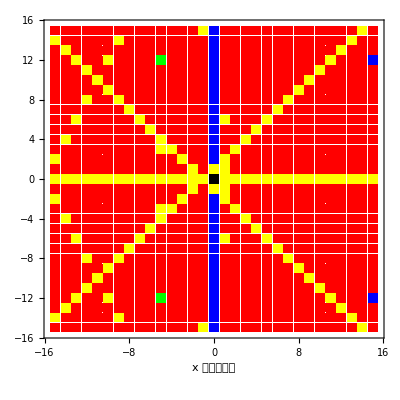

```mathematica
GaloisPlot[15]//TT
```

```mathematica
GaloisGroup[x^5-5x+12]
```

{DihedralGroup[10]}

```mathematica
Solve[x^5-5x+12==0,x]
```

{{x→Root[12-5 #1+#1^5&,1]},{x→Root[12-5 #1+#1^5&,2]},{x→Root[12-5 #1+#1^5&,3]},{x→Root[12-5 #1+#1^5&,4]},{x→Root[12-5 #1+#1^5&,5]}}

总运行时:  3.11073

CPU 时间:  3.10938

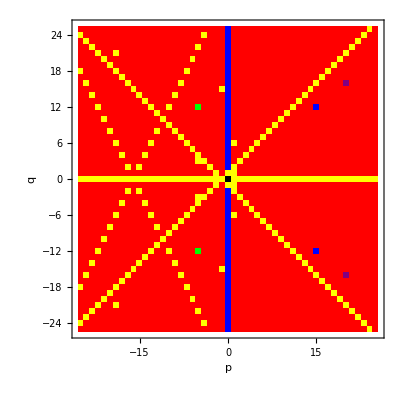

```mathematica
GaloisPlot[25]//TT
```

总运行时:  14.2074

CPU 时间:  14.2188

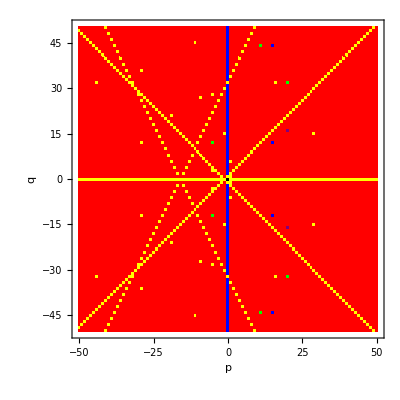

```mathematica
GaloisPlot[50]//TT
```

```mathematica
GaloisPlot[50]//Timing
```

{458.01 Second,⁃Graphics⁃}

```mathematica
GaloisGroup[x^5+x^4-3x^2+3x+1]
```

{SymmetricGroup[5]}